```mathematica
FetchData[filename_]:=  Import[NotebookDirectory[]<>"../data/simulation/"<>filename];
ExportData[filename_, data_]:= Export[NotebookDirectory[]<>"../data/simulation/"<>filename, data];
```

## Generate agents

```mathematica
ClearAll["GenerateAgentsUniform"];
GenerateAgentsUniform[nAgents_,nNodes_]:=Table[RandomInteger[{1,nNodes}],nAgents];

ClearAll["GenerateOccupanciesUniform"];
GenerateOccupanciesUniform[nAgents_,nNodes_]:=Module[{occupancies},
occupancies = Table[0, nNodes];

Do[occupancies[[RandomInteger[{1, nNodes}]]]++, nAgents];

occupancies
];
```

## Prepare data

```mathematica
ClearAll["ComputeCumRatesAndLinks"];
ComputeCumRatesAndLinks[g_, w_, arrayStart_:0] := Module[{maxLinks, nodeCount,lists},
maxLinks = Max@VertexDegree@g;
nodeCount = Length@w;

On[Assert];
lists = ParallelTable[Module[{col, cumulativeRate, nodeRates, nodeLinks, i, rate},
col = Normal@w[[j]];

Assert[Total@col == 1];

cumulativeRate = 0;
nodeRates = {};
nodeLinks = {};

(*Compute cumulative rates so random choice doesn't have to loop through the whole matrix*)
Assert[Length@col == nodeCount];
For[i = 1, i <= nodeCount, i++,
rate = col[[i]];
If[rate == 0, Continue[]];

cumulativeRate += rate;
AppendTo[nodeRates, cumulativeRate];
AppendTo[nodeLinks, i-(1-arrayStart)]; (* C++ counts from zero. Mathematica from 1.*)
];


Assert[Max@nodeRates == 1];
Assert[Length@nodeRates <= maxLinks];
Assert[Length@nodeLinks <= maxLinks];
Assert[Length@nodeRates == Length@nodeLinks];

(*Since array has to be square, we fill it with invalid values*)
While[Length@nodeRates < maxLinks,
AppendTo[nodeRates, -1];
AppendTo[nodeLinks, -1];
];

{nodeRates, nodeLinks}
], {j, 1, nodeCount}];

Return[Transpose@lists];
];
```

### Prepare data for CUDA sim

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-naive.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-naive.csv", rateList];
ExportData["link-list.csv", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-speed.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-speed.csv", rateList];
ExportData["link-list-speed.csv", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-morning.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-time.csv", rateList];
ExportData["link-list-time-morning.csv", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-evening.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-time.csv", rateList];
ExportData["link-list-time-evening.csv", linkList];
```

```mathematica
c= FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

ExportData["thresholds.csv", c];
ExportData["flows.csv", f];
```

### Prepare data for mathematica sim

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-naive.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list.mx", rateList];
ExportData["link-list.mx", linkList];
```

Set::shape: Lists {rateList,linkList} and ComputeCumRatesAndLinks[FetchData[g.mx],FetchData[w-naive.mx],1] are not the same shape.

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-speed.mx"];
	
{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-speed.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-speed-nonstationary.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-speed-nonstationary.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-morning.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-time-morning.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-evening.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-time-evening.mx", rateList];
ExportData["link-list.mx", linkList];
```

## Multiple node sim

```mathematica
ClearAll["SimulateMulti"];
SimulateMulti[cumulativeRates_, linkList_, thresh_, nodeFlows_,  nAgents_, maxSteps_, nVaccines_ : 0, dt_:1] := 
Module[{nNodes, t, ExecuteNode, nodeOccupancies, nodeThresholds},
nodeThresholds = thresh;
nNodes = Length[cumulativeRates];
If[nNodes != Length[nodeThresholds], Return[$Failed]];
If[nNodes != Length[nodeFlows], Return[$Failed]];

For[i = 1, i <=nVaccines, i++, Module[{node, choice, linkId, destNode},
node = RandomInteger[{1, nNodes}];
choice = RandomReal[];
linkId =SelectFirst[cumulativeRates[[node]],choice <= #& -> "Index", -1];
Assert[linkId != -1];
destNode = linkList[[node, linkId]];

nodeThresholds[[destNode]] = +Infinity;
]
];


nodeOccupancies = {GenerateOccupanciesUniform[nAgents, nNodes]};

ExecuteNode [nodeId_, t_] := Module[{maxCarsToMove, carsInNode, carsToMove, choices, links},
maxCarsToMove = nodeFlows[[nodeId]]  * dt;
carsInNode = nodeOccupancies[[t, nodeId]];
choices = cumulativeRates[[nodeId]];
links = linkList[[nodeId]];

carsToMove = Floor@Min[{carsInNode, maxCarsToMove}];

(*ParallelDo here slows down by a lot due to memory overhead sigh*)
Do[
Module[{choice, linkId, destNode},
choice = RandomReal[];
linkId =SelectFirst[choices,choice <= #& -> "Index", -1];
Assert[linkId != -1];
destNode = links[[linkId]];

If[nodeThresholds[[destNode]] >= nodeOccupancies[[t, destNode]], 
nodeOccupancies[[t+1, destNode]]++;
nodeOccupancies[[t+1, nodeId]]--;
];
], carsToMove];
];

For[t=1, t<=maxSteps,  t++,
AppendTo[nodeOccupancies, nodeOccupancies[[-1]]];
Do[ExecuteNode[i, t], {i, 1, nNodes}];

Assert[Total[nodeOccupancies[t] == nAgents]];
];

nodeOccupancies
];
```

### Simulations

```mathematica
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

n = 20000;
M = Length@c;
t = 50;
sampleCount = 20;
```

#### Null model

```mathematica
results = Table[GenerateOccupanciesUniform[n, M] ,sampleCount];
ExportData["results-null.mx", results];
```

#### Naive

```mathematica
{rateList, linkList} = {FetchData["rate-list.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t], sampleCount, Method->"FinestGrained"];

ExportData["results-naive.mx", results];
```

#### Naive bracketed

```mathematica
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

Monitor[Table[
M = Length@c;
t = 100;
sampleCount = 4;

{rateList, linkList} = {FetchData["rate-list.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t, 0, dt], sampleCount, Method->"FinestGrained"];

ExportData["results-naive-"<>ToString[n]<>"-"<>ToString[dt]<>".mx", results];
, {dt, 1, 61, 5}, {n, 20000, 20000, 5000}], ProgressIndicator[dt, {1, 61}]]
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

#### Naive length bracketed

```mathematica
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

Monitor[Table[
M = Length@c;
sampleCount = 4;
dt = 5;

{rateList, linkList} = {FetchData["rate-list.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t, 0, dt], sampleCount, Method->"FinestGrained"];

ExportData["results-naive-"<>ToString[n]<>"-"<>ToString[dt]<>"-"<>ToString[t]<>".mx", results];
, {t, 10, 200, 5}, {n, 20000, 20000, 5000}], ProgressIndicator[t, {10, 200}]]
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

#### Speed

```mathematica
{rateList, linkList} = {FetchData["rate-list-speed.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t], sampleCount, Method->"FinestGrained"];

ExportData["results-speed.mx", results];
```

#### Speed bracketed

```mathematica
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

Monitor[Table[
M = Length@c;
t = 100;
sampleCount = 4;

{rateList, linkList} = {FetchData["rate-list-speed.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t, 0, dt], sampleCount, Method->"FinestGrained"];

ExportData["results-speed-"<>ToString[n]<>"-"<>ToString[dt]<>".mx", results];
, {dt, 1, 31, 5}, {n, 5000, 30000, 5000}], ProgressIndicator[dt, {1, 31}]]
```

{{Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null}}

#### Time morning

```mathematica
{rateList, linkList} = {FetchData["rate-list-time-morning.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t], sampleCount, Method->"FinestGrained"];

ExportData["results-time-morning.mx", results];
```

#### Time evening

```mathematica
{rateList, linkList} = {FetchData["rate-list-time-evening.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t], sampleCount, Method->"FinestGrained"];

ExportData["results-time-evening.mx", results];
```

## Avalanche size

```mathematica
(*On[Assert]*)

ClearAll["Pop"];
SetAttributes[Pop,HoldFirst];
Pop[list_]:=With[{item=list[[1]]},list=Delete[list,1];item];

ClearAll["SimulateSingle"];
SimulateSingle[rateMatrix_, nodeThresholds_, nAgents_, maxSteps_] := Module[{MoveAgents, AreThereFailures , ComputeAvalancheSize, i, nNodes,  carCountsByNode, startingAgentPositions, agentPositions, possibleAgentPositions, failedNodes},
nNodes = Length[rateMatrix];
If[nNodes != Length[nodeThresholds], Return[$Failed]];

startingAgentPositions = GenerateAgentsUniform[nAgents, nNodes];

possibleAgentPositions = Table[i, {i, 1, nNodes}];
agentPositions = startingAgentPositions;	

MoveAgents[] := Module[{},
agentPositions = (
Assert[Total[rateMatrix[[;;, #]]] == 1];
RandomChoice[rateMatrix[[;;, #]]->possibleAgentPositions ]
) &/@ agentPositions;
];

AreThereFailures[] := Module[{},
carCountsByNode = Count[agentPositions, #] &/@ Table[i, {i, 1, nNodes}];
failedNodes = Append[(Transpose@Position[# < 0 &/@ (nodeThresholds -carCountsByNode ), True]), {}][[1]];

If[Length[failedNodes]>0, Return[True]];
False
];

ComputeAvalancheSize[node_]:=Module[{avalancheSize,carCount,avalancheCarCounts,adjacentNodes,nodesToCheck,lockedNodes,currentNode,newNode,transitionProbabilities},nodesToCheck={node};
lockedNodes={};
avalancheCarCounts=carCountsByNode;
While[Length@nodesToCheck>0,currentNode=Pop[nodesToCheck];
Assert[avalancheCarCounts[[currentNode]]>0,"carCount"];
If[nodeThresholds[[currentNode]]-avalancheCarCounts[[currentNode]]>=0,Continue[]];
AppendTo[lockedNodes,currentNode];
If[Length@lockedNodes==nNodes,Break[]];
transitionProbabilities=Normal@rateMatrix[[currentNode]];
(transitionProbabilities[[#]]=0)&/@lockedNodes;
(*If there is nowhere to go,we just lock this node and no transfer*)If[Total@transitionProbabilities==0,Continue[];];
transitionProbabilities/=Total[transitionProbabilities];
For[carCount=avalancheCarCounts[[currentNode]],carCount>0,carCount--,Assert[nNodes==Length@transitionProbabilities,"nNodes"];
newNode=RandomChoice[transitionProbabilities->Table[x,{x,1,nNodes}]];
Assert[newNode!=currentNode,"currentNode"];
Assert[!MemberQ[lockedNodes,newNode],"lockedNodes"];
If[!MemberQ[nodesToCheck,newNode],AppendTo[nodesToCheck,newNode]];
avalancheCarCounts[[newNode]]++;
avalancheCarCounts[[currentNode]]--;];];
Assert[Total[avalancheCarCounts]==Total[carCountsByNode]];
Return[{node,Length@lockedNodes}];];

For[i=1, i<=maxSteps,  i++, 
MoveAgents[];

If[!AreThereFailures[], Continue[]];
Break[];
];

If[Length@failedNodes == 0, Return[{}]];

Map[ComputeAvalancheSize, failedNodes]
];
```

```mathematica
w = FetchData["w-naive.mx"];
c = FetchData["thresholds.mx"];
n = 20000;
f = FetchData["flows.mx"];

t = 20;
sampleCount = 10;

(*;;,;;,2 Selects avalanche size,;;,;;,1 selects start node*)
avalancheSizes= Flatten[ParallelTable[SimulateSingle[w,c,n,t][[;;, 2]],sampleCount, Method->"FinestGrained"]];
```

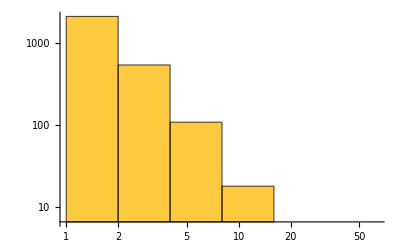

```mathematica
Histogram[avalancheSizes,{PowerRange[1, 100, 2]},  ScalingFunctions->{"Log", "Log"}, PlotRange->Full ]
```

## Immunization 1 (immunizing nodes)

#### Time morning bracketed

```mathematica
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

Table[
M = Length@c;
t = 25;
sampleCount = 10;

{rateList, linkList} = {FetchData["rate-list-time-morning.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t], sampleCount, Method->"FinestGrained"];

ExportData["results-time-morning-"<>ToString[n]<>".mx", results];
, {n, 4000, 32000, 4000}]
```

#### Time morning with immunization bracketed

```mathematica
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

Do[
M = Length@c;
t = 25;
sampleCount = 10;

{rateList, linkList} = {FetchData["rate-list-time-morning.mx"], FetchData["link-list.mx"]};

results = ParallelTable[Last@SimulateMulti[rateList, linkList, c, f, n, t, 900], sampleCount, Method->"FinestGrained"];

ExportData["results-time-morning-immunized-900-"<>ToString[n]<>".mx", results];
, {n, 4000, 32000, 4000}]
```

## Immunization 2

Congested nodes are cut off from the network

```mathematica
ClearAll["SimulateMulti"];
SimulateMulti[cumulativeRates_, linkList_, thresh_, nodeFlows_,  nAgents_, maxSteps_, nVaccines_ : 0] := 
Module[{nNodes, t, ExecuteNode, nodeOccupancies, nodeThresholds},
nodeThresholds = thresh;
nNodes = Length[cumulativeRates];
If[nNodes != Length[nodeThresholds], Return[$Failed]];
If[nNodes != Length[nodeFlows], Return[$Failed]];

For[i = 1, i <=nVaccines, i++, Module[{node, choice, linkId, destNode},
node = RandomInteger[{1, nNodes}];
choice = RandomReal[];
linkId =SelectFirst[cumulativeRates[[node]],choice <= #& -> "Index", -1];
Assert[linkId != -1];
destNode = linkList[[node, linkId]];

nodeThresholds[[destNode]] = +Infinity;
]
];


nodeOccupancies = {GenerateOccupanciesUniform[nAgents, nNodes]};

ExecuteNode [nodeId_, t_] := Module[{maxCarsToMove, carsInNode, carsToMove, choices, links},
maxCarsToMove = nodeFlows[[nodeId]];
carsInNode = nodeOccupancies[[t, nodeId]];
If[carsInNode > thresholds[[nodeId]], Return[]];
choices = cumulativeRates[[nodeId]];
links = linkList[[nodeId]];

carsToMove = Floor@Min[{carsInNode, maxCarsToMove}];

(*ParallelDo here slows down by a lot due to memory overhead sigh*)
Do[
Module[{choice, linkId, destNode},
choice = RandomReal[];
linkId =SelectFirst[choices,choice <= #& -> "Index", -1];
Assert[linkId != -1];
destNode = links[[linkId]];

If[nodeThresholds[[destNode]] >= nodeOccupancies[[t, destNode]], 
nodeOccupancies[[t+1, destNode]]++;
nodeOccupancies[[t+1, nodeId]]--;
];
], carsToMove];
];

For[t=1, t<=maxSteps,  t++,
AppendTo[nodeOccupancies, nodeOccupancies[[-1]]];
Do[ExecuteNode[i, t], {i, 1, nNodes}];

Assert[Total[nodeOccupancies[t] == nAgents]];
];

nodeOccupancies
];
```